## Подготовка

```mathematica
g = Range[1,8, 1];
e = Range[9, 24,1];
e = Delete[e, {{14-8}, {15-8}, {20-8}}]; (* при q=1 неактивны *)

τ=1 (* τ *);
τTrue = 27.2  10^-9;(* c *)
λ0 = 670.951 10^-9; (* м *)
cLight = 3 10^8 ;(* м/c *)

ω0 = 2 π cLight/λ0 τTrue;
ω1 = 2π 803.5 10^6 τTrue;
ω2 = 2π 9.2 10^6 τTrue;
ω3 = 2π 6.2 10^6 τTrue;
ω4 = 2π  3.1 10^6 τTrue;

ClearAll[CRabi];
CRabi[{F2_, mF2_},{F1_, mF1_}, q_ : 1, 
Ι_ : 3/2, S_ : 1/2, J1_ : 1/2, J2_ : 3/2, L1_ : 0, L2_ : 1] := 
(-1)^(1/2 q(1+q) + 1 + 2 F1 - mF1 + Ι + J2 +S +L2 + J1)√((2 F1 + 1)(2 F2 + 1)(2 J1 +1)(2 J2 + 1)(2 L1 + 1)) ThreeJSymbol[{F1, -mF1},{1,q},{F2, mF2}] SixJSymbol[{J1,F1, Ι},{F2,J2,1}] SixJSymbol[{L1,J1,S},{J2,L2,1}] /; q + mF2 - mF1 == 0 && Abs[F1-F2] ≤ 1;
CRabi[{F2_, mF2_}, {F1_, mF1_}, q_ : 1, 
Ι_ : 3/2, S_ : 1/2, J1_ : 1/2, J2_ : 1/2, L1_ : 0, L2_ : 1] := 0;

ClearAll[objFmF];
objFmF = <|
1->{1, -1},2->{1,0},3->{1, 1} ,
4->{2, -2},5->{2, -1},6->{2, 0},7->{2, 1},8->{2, 2},
9->{3, -3},10->{3, -2},11->{3, -1},12->{3, 0},13->{3, 1},14->{3, 2},15->{3, 3},
16->{2, -2},17->{2, -1},18->{2, 0},19->{2, 1},20->{2, 2},
21->{1, -1},22->{1, 0},23->{1, 1},
24->{0, 0}
|>;
objωR = <|
1->0,2->0,3->0 ,
4->ω1,5->ω1,6->ω1,7->ω1,8->ω1,
9->0,10->0,11->0,12->0,13->0,14->0,15->0,
16->ω2,17->ω2,18->ω2,19->ω2,20->ω2,
21->ω3,22->ω3,23->ω3,
24->ω4
|>;

ClearAll[GetωR, GetCRabi,GetΩRabi];
GetωR[β_, α_] := GetωR[β, α] = ω0 + objωR[β] - objωR[α];
GetCRabi[β_, α_] :=GetCRabi[β, α] = CRabi[objFmF[β],objFmF[α]];
GetΩRabi[β_, α_, s_:1] :=0.17/τ √s GetCRabi[β, α]; 

ClearAll[SCALE];
SCALE[β_]:=SCALE[β]= Total@Map[GetCRabi[β,#]^2&, g]; 
ClearAll[SCALE2];
SCALE2[α_]:= SCALE2[α]=Total@Map[GetCRabi[#,α]^2&, e]; 

ListρRe = Flatten@Outer[ρRe,e,g]; 
ListρIm = Flatten@Outer[ρIm,e,g]; 
Listρα = Map[ρ[#, #]&, g]; 
Listρβ = Map[ρ[#, #]&, e]; 
ListFull = Join[Listρα, Listρβ, ListρIm, ListρRe];

varsI = ListFull;
varsII = Table[Unique[], {i, 1, Length[varsI], 1}];
subsI = Table[varsI[[i]]-> varsII[[i]], {i, 1, Length@varsI, 1}];
subsII = Table[varsII[[i]]-> varsI[[i]], {i, 1, Length@varsI, 1}];

ClearAll[GetGroundEvol, GetExitedEvol, GetReDiagonalEvol, GetImDiagonalEvol];
GetGroundEvol[ζ_, s_, α_] := 2ζ Total@Map[ρIm[#, α]GetΩRabi[#, α, s]&, e] + 1/τ Total@Map[ ρ[#, #]N@(GetCRabi[#, α]^2)&, e];
GetExitedEvol[ζ_,s_, β_] := -2 ζ Total@Map[ρIm[β, #]GetΩRabi[β, #, s]&, g] - 1/τ ρ[β, β]SCALE[β];
GetReDiagonalEvol[δ_,s_, β_, α_] := (GetωR[β, α]-ω0 - δ)ρIm[β, α] -1/(2τ)ρRe[β, α]SCALE[β];
GetImDiagonalEvol[δ_,s_, ζ_, β_, α_] := ζ GetΩRabi[β, α, s](ρ[β, β] - ρ[α, α])-(GetωR[β, α]-ω0 - δ)ρRe[β, α] -1/(2τ)ρIm[β, α]SCALE[β];

ClearAll[EQS]; 
EQS = Join[
FullSimplify@Map[GetGroundEvol[ζ0,s0, #]&, g], 
FullSimplify@Map[GetExitedEvol[ζ0,s0, #]&, e], 
FullSimplify@Flatten@Outer[GetImDiagonalEvol[δ0,s0, ζ0, #1, #2]&,e,g] ,  
FullSimplify@Flatten@Outer[GetReDiagonalEvol[δ0, s0, #1, #2]&,e,g] ];

ClearAll[GetCoefs];
GetCoefs[δ_, s_:1, ζ_:1]:=Module[{eqsI, eqsII, coefs, coefsSA},
eqsI = EQS/.{ζ0 -> ζ,δ0-> δ, s0-> s};
eqsII = eqsI /. subsI;
coefs = Normal@CoefficientArrays[eqsII,varsII][[2]] ;
coefsSA = SparseArray[coefs];
coefsSA
]

ClearAll[GetCoefsM]; (* сохраняет значения *)
GetCoefsM[δ_, s_:1, ζ_:1]:=GetCoefsM[δ, s, ζ] = Module[{eqsI, eqsII, coefs, coefsSA},
eqsI = EQS/.{ζ0 -> ζ,δ0-> δ, s0-> s};
eqsII = eqsI /. subsI;
coefs = Normal@CoefficientArrays[eqsII,varsII][[2]] ;
coefsSA = SparseArray[coefs];
coefsSA
]

ClearAll[GetPop];
GetPop[f_] := Module[{g1, g2, e0, e1,e2,e3},
g1 = Total[f[[ 1;;3]]];
g2 = Total[f[[ 4;;8]]];
e3 = Total[f[[ 9;;13]]];
e2 = Total[f[[ 14;;17]]];
e1 = Total[f[[ 18;;20]]];
e0 = Total[f[[ 21]]];
{g1, g2, e3, e2, e1, e0}
];

ClearAll[GetLevels];
GetLevels[δ_, s_, ζ_:1, Ν_:100, tMax_:50] := Module[{res,data, coefsSA,exp},
coefsSA =GetCoefs[δ, s, ζ];
exp = MatrixExp[tMax coefsSA];
data = Table[
IC = Join[Normalize[ RandomReal[{0, 1}, 8], Total], ConstantArray[0, Length@varsI-8]];
GetPop[exp.IC]
, {i, 1, Ν}];
res = 1/Ν Total[data, {1}] ;
res
];

ClearAll[GetLevels2];
GetLevels2[δ_, s_, ζ_:1, Ν_:100] := Module[{res,data, coefsSA,exp, IC},
coefsSA =GetCoefs[δ, s, ζ];
exp = MatrixExp[50coefsSA];
data = Table[
IC = Join[Normalize[ RandomReal[{0, 1}, 8], Total], ConstantArray[0, Length@varsI-8]];
exp.IC
, {i, 1, Ν}];
res = 1/Ν Total[data, {1}] ;
res
];
```

```mathematica
inds = {1,2,3,4,5,6,7,8,9,10,11,12,13,16,17,18,19,21,22,23,24};
ClearAll[GetAbs];
GetAbs[f_]:=Total@Table[SCALE2[inds[[χ]]]f[[χ]], {χ, 1, 8}]-Total@Table[SCALE[inds[[χ]]]f[[χ]], {χ, 9, 21, 1}];

ClearAll[GetLevels3];
GetLevels3[δ_, s_, IC_, ζ_:1, tMax_:2000] := Module[{res,data, coefsSA,exp},
coefsSA =GetCoefsM[δ, s, ζ];
exp = MatrixExp[tMax coefsSA];
GetPop[exp.IC]
];

o2n = 10^-6 1/τTrue 1/(2 π);
```

```mathematica
ClearAll[GetLevelsM];
GetLevelsM[δ_, s_, ζ_:1, Ν_:100, tMax_:50] := Module[{res,data, coefsSA,exp},
coefsSA =GetCoefsM[δ, s, ζ];
exp = MatrixExp[tMax coefsSA];
data = Table[
IC = Join[Normalize[ RandomReal[{0, 1}, 8], Total], ConstantArray[0, Length@varsI-8]];
GetPop[exp.IC]
, {i, 1, Ν}];
res = 1/Ν Total[data, {1}] ;
res
];
```

## Распределение по уровням и оценка поглощения

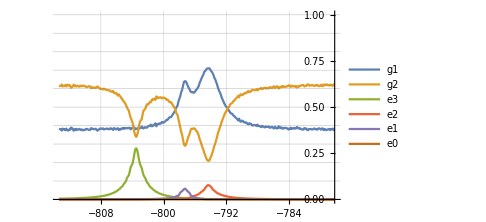

```mathematica
width = 3;
δs = Range[-136-width, -136+width,0.02];
reg1= {{-136-width, -136+width}o2n, {0, 1}};
reg2= {{-width, +width}};
vals = Transpose@ParallelMap[GetLevels[#, 4, 1, 1000, 100]&,δs];
ListLinePlot[Map[Transpose@{δs o2n, #}&, vals], PlotRange->reg1, PlotLegends->{"g1", "g2", "e3", "e2","e1", "e0"}, GridLines->{Automatic, Range[0,1, 0.1]}, ImageSize->Medium]
```

```mathematica
(*δs = Range[-150, 10,0.1];
abs = ParallelMap[GetAbs[GetLevels2[#, 2, 1, 5000]]&,δs];
ListLinePlot[abs, PlotRange->Full, GridLines->{Automatic, Range[0, 1, 0.1]}]*)
```

## Эволюция во времени

### Развертка по Δν

```mathematica
ClearAll[GetImage];
GetImage[tMax_] := Module[{δs, vals, IC},
IC = Join[ConstantArray[1, 8]/8, ConstantArray[0, Length@varsI-8]];
δs = Range[-40, 20,0.2];
vals = Transpose@ParallelMap[GetLevels3[#, 2, IC, 1, tMax]&,δs];
Multicolumn[{
ListLinePlot[vals[[;;2]], PlotRange->{Automatic, {0,1}}, PlotLegends->{"g1", "g2"}, GridLines->Automatic, ImageSize->Medium],
ListLinePlot[vals[[3;;]], PlotRange->{Automatic, {0,0.5}}, PlotLegends->{"e3", "e2","e1", "e0"}, GridLines->Automatic, ImageSize->Medium]
}, {2,1}]]
```

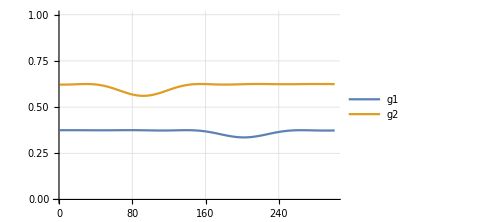
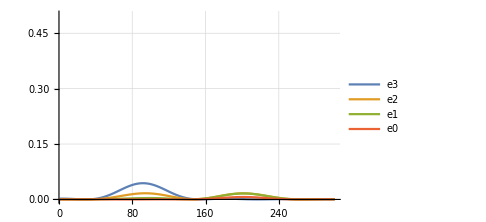

```mathematica
GetImage[0.5]
```

```mathematica
imgs = Join[imgs, Map[GetImage, Range[10.1, 15, 0.1]]];
```

```mathematica
ListAnimate[imgs]
```

```mathematica
Export[NotebookDirectory[]<>"dopler_evol.gif", imgs, "DisplayDurations"-> 1/20]
```

D:\git\notes_6sem\qmec\report_2\mathematica\dopler_evol.gif

### Фиксированный Δν

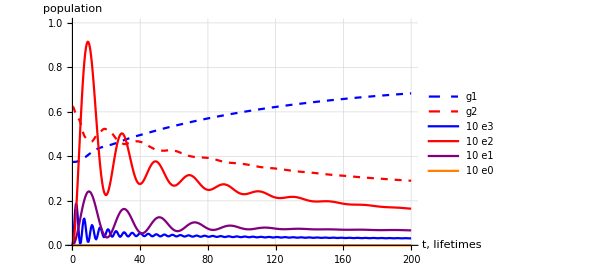

```mathematica
ScaleVec = DiagonalMatrix[Join[{1, 1}, 10{1,1,1,1}]];
IC = Join[ConstantArray[1, 8]/8, ConstantArray[0, Length@varsI-8]];
τs = Range[0, 200,0.5];
vals = Transpose@ParallelMap[ScaleVec.GetLevels3[-136, 4 , IC, 1, #]&,τs];
ListLinePlot[Map[Transpose@{τs, #}&, vals], PlotRange->{Automatic, {0,1}}, PlotLegends->{"g1", "g2", "10 e3", "10 e2","10 e1", "10 e0"}, GridLines->Automatic, ImageSize->Medium,AxesLabel->{"t, lifetimes", "population"}, PlotStyle->{
{Dashed, Blue}, {Dashed, Red}, 
{Blue}, {Red}, {Purple}, {Orange}
}]
```

## Доплер

```mathematica
c = 3. 10^8  ;
v = 100. ;
β = v/c;
dt = (0.01 10^-9)/τTrue;
Print["β = ", β]
Print["dt = ", dt]
Print["Δφ = ", ω0 β dt]
Print["требуется шагов = ", 1/dt]
```

β = 3.33333×10^-7

dt = 0.000367647

Δφ = 0.0093646

требуется шагов = 2720.

В силу dt << τ можем не считать матричную экспоненту, а рассматривать эволюцию методом Эйлера.

```mathematica
(*ζ = RandomReal[];*)
m1 = GetCoefs[δ, s, ζ]; //AbsoluteTiming
m2 = GetCoefsM[δ, s, ζ]; //AbsoluteTiming
m2-m1 //Norm
```

{0.0291007,Null}

{5.7×10^-6,Null}

0.

```mathematica
ClearAll[DoStep];
DoStep[δ_, s_, v_, fC_] := Module[{f, num, coefsSA, EvolMat, coef},
num = fC[[1]];
f = fC[[2;;]];
coef =  ω0  v/c dt;
coefsSA =GetCoefsM[δ, s, Cos[coef num]];
Join[{num+1}, f + dt coefsSA.f]
];
```

```mathematica
num = 0;
coef =  ω0  v/c dt;
coef = Round[(2π)/coef, 1];
coef = 10;
δ = -136;
s = 4;
v = 100;
AbsoluteTiming[Map[GetCoefsM[δ, s, Cos[(2π)/coef #]]&, Range[0, 1000, 1]];][[1]]
```

0.209295

```mathematica
IC = N@Join[ConstantArray[1, 8]/8, ConstantArray[0, Length@varsI-8]];
state = Join[{num},IC];
AbsoluteTiming[story = NestList[DoStep[δ, s, v, #]&, state, 5000];][[1]]
```

0.433549

```mathematica
story = Map[GetPop, story[[;;, 2;;]]];
```

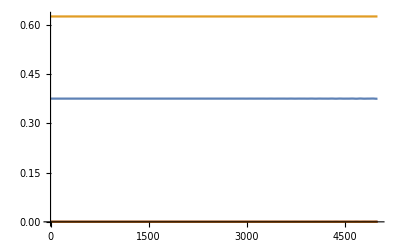

```mathematica
ListLinePlot[Transpose@story, PlotRange->Full]
```

## Псевдодоплер

```mathematica
Na = 6 10^23;
c = 3. 10^8  ;
mLi = 7 10^-3 / Na;
T = 273 + 300;
kB = 1.38 10^-23;
ClearAll[MaxwellProb];
MaxwellProb[v_] := √(mLi/(2 π kB T)) Exp[- (mLi v^2)/(2 kB T)];
```

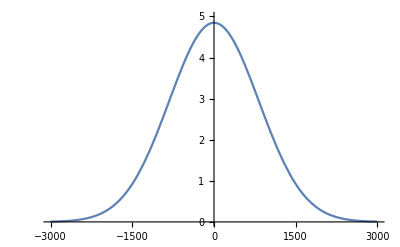

```mathematica
Plot[10^4 MaxwellProb[v], {v,-3000, 3000}, PlotRange->{Automatic, {0, 5 }}]
```

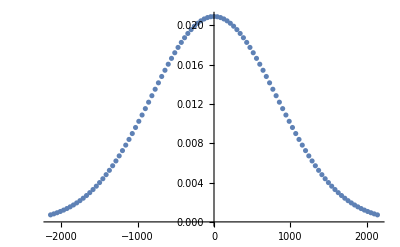

```mathematica
Νv = 50;
vs = 3/(2 Νv)√((3 kB T)/mLi)Range[-Νv, Νv, 1];
Pvs = Normalize[Map[MaxwellProb, vs], Total];
ListPlot[Transpose[{vs, Pvs}]]
```

```mathematica
ClearAll[GetVLevels, GetAverageLevels];
GetVLevels[δL_, {pv_, v_}] := pv GetLevelsM[δL + ω0 v/c, (*s*)40, (*ζ*)1, (*Ν*)200, (*tMax*)200];
GetAverageLevels[δL_] := Total[ParallelMap[GetVLevels[δL, #]&, Transpose[{Pvs, vs}]], {1}];
```

```mathematica
ScaleVec = DiagonalMatrix[Join[{1, 1}, 1{1,1,1,1}]];
dists = Map[GetAverageLevels[#]&, Range[-700, 500, 1]];
```

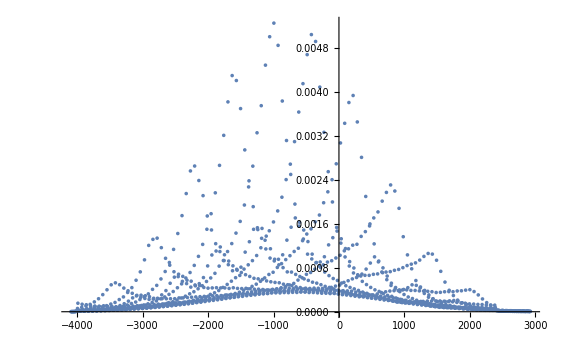

```mathematica
ListPlot[Transpose[{o2n Range[-700, 500, 1], Map[Total[#[[3;;4]]]&, dists]}], PlotRange->Full]
```

```mathematica
Compile
```